# < A Project Title >

< Shivain Vij>

< Philip Maymin >
Finding the maximum return rate for a unit of a cryptocurrency
Variance
Cryptocurrency portfolio tracker
Look at cryptocurrency prices since they go up and down a lot


Predict how much money a cryptocoin can make and how long it will last
How much money it goes up by before it peaks and comes back down.
Why certain peaks are larger than others

```mathematica
BTCData= (*Insert[*)SemanticImport["https://api.blockchain.info/charts/market-price?format=csv"](*, {"Date", "Value"}, 1] *)(*Import data from online CSV and add header row*)
```

Dataset[<>]

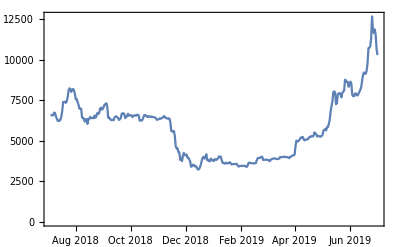

```mathematica
DateListPlot[BTCData]
```

Put all scrap code below:

```mathematica
BTCData[[#+1]][[1]]&[1, 2, 3]
```

```mathematica
DateList[{Table[BTCData[[x+1]][[1]], {x, 5}],{"MonthName","Day","Year"}}]
```